Code to reproduce results from Aguirre et al. “Idiosyncratic and dose-dependent epistasis drives variation in tomato fruit size”. This notebook assumes that the file containing the raw locule counts “Aguirre-etal-epistasis-sourcedata.xlsx” is in the same directory as the notebook file itself.

## Import data

Read the data from the excel spreadsheet and label data from each page of the spreadsheet by the corresponding field season

```mathematica
SetDirectory[NotebookDirectory[]];
seasons={"WestneckSummer2021","FLAFall2021","FLASpring2021","WestneckSummer2020","FLASpring2020","DoubleNullCompiled","FLASpring2022"};
data=Select[Flatten[Table[
Append[#,seasons[[i]]]&/@Import["Aguirre-etal-Table-S3.xlsx",{"Data",i}][[4;;,{1,2}]],
{i,7}],1],#[[1]]!=""&];
```

Parse strings encoding genotypes and convert to vectorized consisting of the allelic state at each locus.

```mathematica
rawgenos=Union[data[[All,1]]];
genos=StringSplit[ToString[#],"/"]&/@rawgenos;
genos=(Table[
If[Length[x]==3,x,
If[x=={"SlwusCR-lc","Slcle9"},{"WT","SlwusCR-lc","Slcle9"},
If[MemberQ[x,"Slcle9"]&&Length[x]==1,{"WT","WT","Slcle9"},
If[MemberQ[x,"SlwusCR-lc"]&&Length[x]==1,{"WT","SlwusCR-lc","WT"},
If[MemberQ[x,"Slcle9"]&&Length[x]>1,Insert[x,"WT",-2],
If[MemberQ[x,"SlwusCR-lc"]&&Length[x]>1,Insert[x,"WT",-1],
Flatten[Insert[x,{"WT","WT"},-1]]]]]]]],
{x,genos}]);
genorules=Table[rawgenos[[i]]->(genos[[i]]),{i,Length[rawgenos]}]
data[[All,1]]=data[[All,1]]/.genorules;
data=Flatten/@data;
```

{Slcle9→{WT,WT,Slcle9},Slclv3fas→{Slclv3fas,WT,WT},Slclv3fas/Slcle9→{Slclv3fas,WT,Slcle9},Slclv3fas/SlwusCR-lc→{Slclv3fas,SlwusCR-lc,WT},Slclv3fas/SlwusCR-lc/Slcle9→{Slclv3fas,SlwusCR-lc,Slcle9},Slclv3Pro-1→{Slclv3Pro-1,WT,WT},Slclv3Pro-11→{Slclv3Pro-11,WT,WT},Slclv3Pro-11/Slcle9→{Slclv3Pro-11,WT,Slcle9},Slclv3Pro-11/SlwusCR-lc→{Slclv3Pro-11,SlwusCR-lc,WT},Slclv3Pro-11/SlwusCR-lc/Slcle9→{Slclv3Pro-11,SlwusCR-lc,Slcle9},Slclv3Pro-12→{Slclv3Pro-12,WT,WT},Slclv3Pro-12/Slcle9→{Slclv3Pro-12,WT,Slcle9},Slclv3Pro-12/SlwusCR-lc→{Slclv3Pro-12,SlwusCR-lc,WT},Slclv3Pro-15→{Slclv3Pro-15,WT,WT},Slclv3Pro-15/Slcle9→{Slclv3Pro-15,WT,Slcle9},Slclv3Pro-15/SlwusCR-lc→{Slclv3Pro-15,SlwusCR-lc,WT},Slclv3Pro-18→{Slclv3Pro-18,WT,WT},Slclv3Pro-18/Slcle9→{Slclv3Pro-18,WT,Slcle9},Slclv3Pro-18/SlwusCR-lc→{Slclv3Pro-18,SlwusCR-lc,WT},Slclv3Pro-1/Slcle9→{Slclv3Pro-1,WT,Slcle9},Slclv3Pro-1/SlwusCR-lc→{Slclv3Pro-1,SlwusCR-lc,WT},Slclv3Pro-2→{Slclv3Pro-2,WT,WT},Slclv3Pro-22→{Slclv3Pro-22,WT,WT},Slclv3Pro-22/Slcle9→{Slclv3Pro-22,WT,Slcle9},Slclv3Pro-22/SlwusCR-lc→{Slclv3Pro-22,SlwusCR-lc,WT},Slclv3Pro-22/SlwusCR-lc/Slcle9→{Slclv3Pro-22,SlwusCR-lc,Slcle9},Slclv3Pro-26→{Slclv3Pro-26,WT,WT},Slclv3Pro-26/Slcle9→{Slclv3Pro-26,WT,Slcle9},Slclv3Pro-26/SlwusCR-lc→{Slclv3Pro-26,SlwusCR-lc,WT},Slclv3Pro-26/SlwusCR-lc/Slcle9→{Slclv3Pro-26,SlwusCR-lc,Slcle9},Slclv3Pro-28→{Slclv3Pro-28,WT,WT},Slclv3Pro-28/Slcle9→{Slclv3Pro-28,WT,Slcle9},Slclv3Pro-28/SlwusCR-lc→{Slclv3Pro-28,SlwusCR-lc,WT},Slclv3Pro-29→{Slclv3Pro-29,WT,WT},Slclv3Pro-29/Slcle9→{Slclv3Pro-29,WT,Slcle9},Slclv3Pro-29/SlwusCR-lc→{Slclv3Pro-29,SlwusCR-lc,WT},Slclv3Pro-29/SlwusCR-lc/Slcle9→{Slclv3Pro-29,SlwusCR-lc,Slcle9},Slclv3Pro-2/Slcle9→{Slclv3Pro-2,WT,Slcle9},Slclv3Pro-2/SlwusCR-lc→{Slclv3Pro-2,SlwusCR-lc,WT},Slclv3Pro-2/SlwusCR-lc/Slcle9→{Slclv3Pro-2,SlwusCR-lc,Slcle9},Slclv3Pro-3→{Slclv3Pro-3,WT,WT},Slclv3Pro-3/Slcle9→{Slclv3Pro-3,WT,Slcle9},Slclv3Pro-3/SlwusCR-lc→{Slclv3Pro-3,SlwusCR-lc,WT},SlwusCR-lc→{WT,SlwusCR-lc,WT},SlwusCR-lc/Slcle9→{WT,SlwusCR-lc,Slcle9},WT→{WT,WT,WT}}

Make lists of the various alleles and the ordering of CLV3 alleles according to their strength.

```mathematica
CLV3alleles=Union[data[[All,1]]]
WUSalleles=Union[data[[All,2]]]
CLE9alleles=Union[data[[All,3]]]
Table[
Mean[
Select[data,#[[1]]==allele&&#[[2]]=="WT"&&#[[3]]=="WT"&][[All,4]]
],{allele,Complement[CLV3alleles]}];
allelicstrengthorder=Ordering[%];
lcSeasons={"WestneckSummer2021","FLAFall2021"};
cle9Seasons={"FLASpring2021","WestneckSummer2020","FLASpring2020"};
```

{Slclv3fas,Slclv3Pro-1,Slclv3Pro-11,Slclv3Pro-12,Slclv3Pro-15,Slclv3Pro-18,Slclv3Pro-2,Slclv3Pro-22,Slclv3Pro-26,Slclv3Pro-28,Slclv3Pro-29,Slclv3Pro-3,WT}

{SlwusCR-lc,WT}

{Slcle9,WT}

## Functions

Function to convert from a vector of residuals to the log likelihood assuming normally distributed errors.

```mathematica
ResidualsToLogLikelihood[vec_]:=Module[{perdatumfunction},
perdatumfunction=Log[PDF[NormalDistribution[0,√(Norm[vec]^2/Length[vec])],#]]&;
Total[(perdatumfunction)/@vec]
]
```

Function to calculate the pairwise interaction coefficient, its 95% confidence interval, and the associated p-value based on vectors of measured phenotypes for the wild-type, two single mutants and the corresponding double mutant, as well as the additive effects of the corresponding non-epistatic model together with their 95% confidence intervals and p-values.

```mathematica
CalculatePairwiseEpistasis[vec_]:=Module[{design,mut1Model,mut1LogLik,mut2Model,mut2LogLik,nonepistaticModel,nonepistaticLogLik,epistaticModel,epistaticLogLik},
(*Format is {WT, Mut1, Mut2, Mut1 Mut2}*)
design=
Flatten[{Transpose[Join[Transpose[ConstantArray[{-1,-1},Length[vec[[1]]]]],{vec[[1]]}] ],
Transpose[Join[Transpose[ConstantArray[{+1,-1},Length[vec[[2]]]]],{vec[[2]]}]],
Transpose[Join[Transpose[ConstantArray[{-1,+1},Length[vec[[3]]]]],{vec[[3]]}]] ,
Transpose[Join[Transpose[ConstantArray[{+1,+1},Length[vec[[4]]]]],{vec[[4]]}]]  },1];

mut1Model=LinearModelFit[design,{mut1},{mut1,mut2}];
mut1LogLik=ResidualsToLogLikelihood[mut1Model["FitResiduals"]];
mut2Model=LinearModelFit[design,{mut2},{mut1,mut2}];
mut2LogLik=ResidualsToLogLikelihood[mut2Model["FitResiduals"]];
nonepistaticModel=LinearModelFit[design,{mut1,mut2},{mut1,mut2}];
nonepistaticLogLik=ResidualsToLogLikelihood[nonepistaticModel["FitResiduals"]];
epistaticModel=LinearModelFit[design,{mut1,mut2,mut1 mut2},{mut1,mut2}];
epistaticLogLik=ResidualsToLogLikelihood[epistaticModel["FitResiduals"]];
Flatten[{
nonepistaticModel["ParameterConfidenceIntervalTableEntries"][[-2,{1,3}]],1-CDF[ChiSquareDistribution[1],2( nonepistaticLogLik-mut2LogLik)],
nonepistaticModel["ParameterConfidenceIntervalTableEntries"][[-1,{1,3}]],1-CDF[ChiSquareDistribution[1],2( nonepistaticLogLik-mut1LogLik)],
epistaticModel["ParameterConfidenceIntervalTableEntries"][[-1,{1,3}]],1-CDF[ChiSquareDistribution[1],2( epistaticLogLik-nonepistaticLogLik)]
}]
(*Output is: coefficient value, lower 95% confidence interval bound, upper 95% confidence interval bound, p-value, for each of mut1 effect, mut2 effect, mut1*mut2 interaction)*)
]
```

Function to calculate the three-way interaction coefficient, its 95% confidence interval, and the associated p-value based on vectors of measured phenotypes for the wild-type, three single mutants, three double mutants and the corresponding triple mutant, as well as the corresponding double-mutant interaction coefficients of the pairwise model and the additive effects of the corresponding non-epistatic model, together with their 95% confidence intervals and p-values.

```mathematica
CalculateThreewayEpistasis[vec_]:=Module[{design,additiveModel,mut1mut2additiveModel,mut1mut3additiveModel,mut2mut3additiveModel, pairwiseModel,minusmut1mut2pairwiseModel,minusmut1mut3pairwiseModel,minusmut2mut3pairwiseModel,threewayModel},
(*Format is {WT, Mut1, Mut2, Mut3, Mut1 Mut2, Mut1 Mut3, Mut2 Mut3, Mut1 Mut2 Mut3}*)
design=
Flatten[{
Transpose[Join[Transpose[ConstantArray[{-1,-1,-1},Length[vec[[1]]]]],{vec[[1]]}] ],
Transpose[Join[Transpose[ConstantArray[{+1,-1,-1},Length[vec[[2]]]]],{vec[[2]]}]],
Transpose[Join[Transpose[ConstantArray[{-1,+1,-1},Length[vec[[3]]]]],{vec[[3]]}]] ,
Transpose[Join[Transpose[ConstantArray[{-1,-1,+1},Length[vec[[4]]]]],{vec[[4]]}]] ,
Transpose[Join[Transpose[ConstantArray[{+1,+1,-1},Length[vec[[5]]]]],{vec[[5]]}]],
Transpose[Join[Transpose[ConstantArray[{+1,-1,+1},Length[vec[[6]]]]],{vec[[6]]}]] ,
Transpose[Join[Transpose[ConstantArray[{-1,+1,+1},Length[vec[[7]]]]],{vec[[7]]}]],
Transpose[Join[Transpose[ConstantArray[{+1,+1,+1},Length[vec[[8]]]]],{vec[[8]]}]]  },
1];
additiveModel=LinearModelFit[design,{mut1,mut2,mut3},{mut1,mut2,mut3}];
mut1mut2additiveModel=LinearModelFit[design,{mut1,mut2},{mut1,mut2,mut3}];
mut1mut3additiveModel=LinearModelFit[design,{mut1,mut3},{mut1,mut2,mut3}];
mut2mut3additiveModel=LinearModelFit[design,{mut2,mut3},{mut1,mut2,mut3}];
pairwiseModel=LinearModelFit[design,{mut1,mut2,mut3,mut1 mut2, mut1 mut3, mut2 mut3},{mut1,mut2,mut3}];
minusmut1mut2pairwiseModel=LinearModelFit[design,{mut1,mut2,mut3, mut1 mut3, mut2 mut3},{mut1,mut2,mut3}];
minusmut1mut3pairwiseModel=LinearModelFit[design,{mut1,mut2,mut3,mut1 mut2, mut2 mut3},{mut1,mut2,mut3}];
minusmut2mut3pairwiseModel=LinearModelFit[design,{mut1,mut2,mut3,mut1 mut2, mut1 mut3},{mut1,mut2,mut3}];
threewayModel=LinearModelFit[design,{mut1,mut2,mut3,mut1 mut2, mut1 mut3, mut2 mut3,mut1 mut2 mut3},{mut1,mut2,mut3}];
Flatten[{
additiveModel["ParameterConfidenceIntervalTableEntries"][[-3,{1,3}]],1-CDF[ChiSquareDistribution[1],2( ResidualsToLogLikelihood[additiveModel["FitResiduals"]]-ResidualsToLogLikelihood[mut2mut3additiveModel["FitResiduals"]])],
additiveModel["ParameterConfidenceIntervalTableEntries"][[-2,{1,3}]],1-CDF[ChiSquareDistribution[1],2( ResidualsToLogLikelihood[additiveModel["FitResiduals"]]-ResidualsToLogLikelihood[mut1mut3additiveModel["FitResiduals"]])],
additiveModel["ParameterConfidenceIntervalTableEntries"][[-1,{1,3}]],1-CDF[ChiSquareDistribution[1],2( ResidualsToLogLikelihood[additiveModel["FitResiduals"]]-ResidualsToLogLikelihood[mut1mut2additiveModel["FitResiduals"]])],

pairwiseModel["ParameterConfidenceIntervalTableEntries"][[-3,{1,3}]],1-CDF[ChiSquareDistribution[1],2( ResidualsToLogLikelihood[pairwiseModel["FitResiduals"]]-ResidualsToLogLikelihood[minusmut1mut2pairwiseModel["FitResiduals"]])],
pairwiseModel["ParameterConfidenceIntervalTableEntries"][[-2,{1,3}]],1-CDF[ChiSquareDistribution[1],2( ResidualsToLogLikelihood[pairwiseModel["FitResiduals"]]-ResidualsToLogLikelihood[minusmut1mut3pairwiseModel["FitResiduals"]])],
pairwiseModel["ParameterConfidenceIntervalTableEntries"][[-1,{1,3}]],1-CDF[ChiSquareDistribution[1],2( ResidualsToLogLikelihood[pairwiseModel["FitResiduals"]]-ResidualsToLogLikelihood[minusmut2mut3pairwiseModel["FitResiduals"]])],

threewayModel["ParameterConfidenceIntervalTableEntries"][[-1,{1,3}]],1-CDF[ChiSquareDistribution[1],2( ResidualsToLogLikelihood[threewayModel["FitResiduals"]]-ResidualsToLogLikelihood[pairwiseModel["FitResiduals"]])]
}]
(*Output is: coefficient value, lower 95% confidence interval bound, upper 95% confidence interval bound, p-value, for each of mut1 effect, mut2 effect, mut2 effect, mut1*mut2 interaction, mut1*mut3 interaction, mut2*mut3 interaction, and the three-way mut1*mut2*mut3 interaction)*)
]
```

Function to extract locule numbers from all experiments that meet certain criteria

```mathematica
SelectFruits[clvvec_,wusvec_,cle9vec_,seasonvec_]:=Select[data,MemberQ[clvvec,#[[1]]]&&MemberQ[wusvec,#[[2]]]&&MemberQ[cle9vec,#[[3]]]&&MemberQ[seasonvec,#[[5]]]&][[All,4]]
```

## Make histograms (Supplemental Figures 1 and 2)

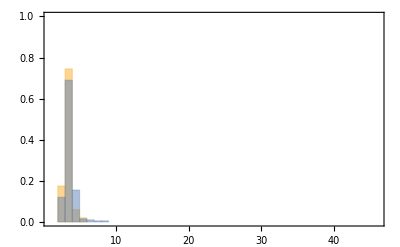
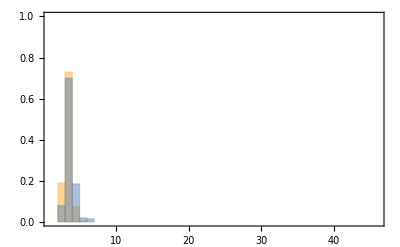
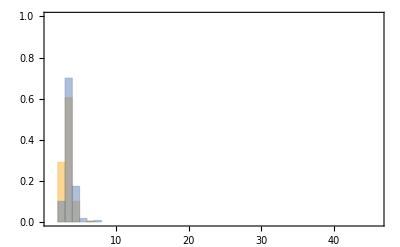
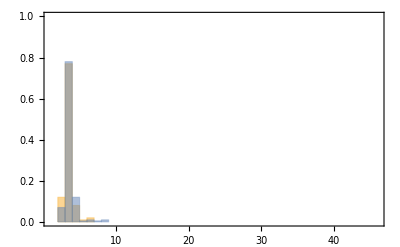
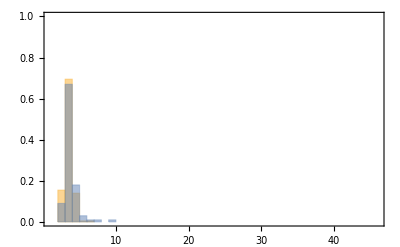
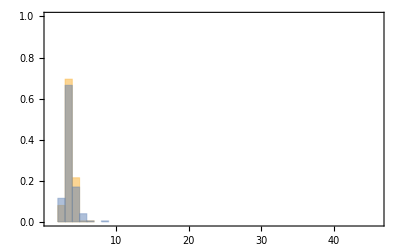
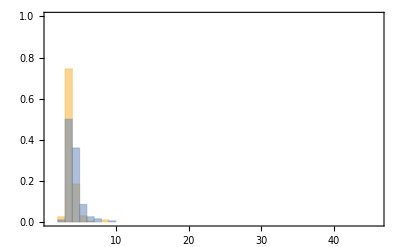
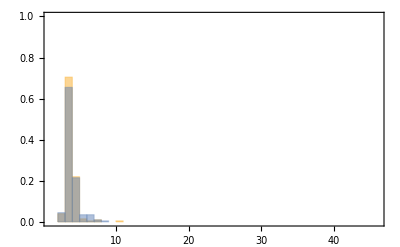
| WestneckSummer2021 | FLAFall2021
WT | -Graphics- | -Graphics-
Slclv3Pro-1 | -Graphics- | -Graphics-
Slclv3Pro-2 | -Graphics- | -Graphics-
Slclv3Pro-3 | -Graphics- | -Graphics-
Slclv3Pro-11 | -Graphics- | -Graphics-
Slclv3Pro-12 | -Graphics- | -Graphics-
Slclv3Pro-15 | -Graphics- | -Graphics-
Slclv3Pro-18 | -Graphics- | -Graphics-
Slclv3fas | -Graphics- | -Graphics-
Slclv3Pro-22 | -Graphics- | -Graphics-
Slclv3Pro-26 | -Graphics- | -Graphics-
Slclv3Pro-28 | -Graphics- | N/A
Slclv3Pro-29 | -Graphics- | -Graphics-

```mathematica
lchistos=Table[
currentcounts={
SelectFruits[{allele},{"WT"},{"WT"},{season}],
SelectFruits[{allele},{"SlwusCR-lc"},{"WT"},{season}]};
If[Length[currentcounts[[1]]]>0||Length[currentcounts[[2]]]>0,
Histogram[currentcounts,{Range[1,46]},"Probability",PlotRange->{{1,46},{0,1}},Frame->True],
"N/A"],
{allele,Part[CLV3alleles,allelicstrengthorder]},{season,{"WestneckSummer2021","FLAFall2021"}}];
Prepend[
Table[Prepend[lchistos[[i]],CLV3alleles[[allelicstrengthorder[[i]]]]],{i,Length[CLV3alleles]}],
Join[{""},{"WestneckSummer2021","FLAFall2021"}]]//TableForm
```

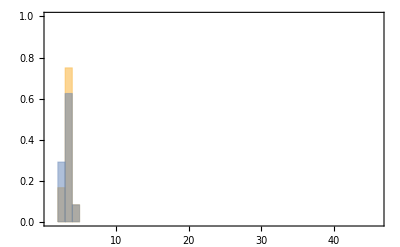
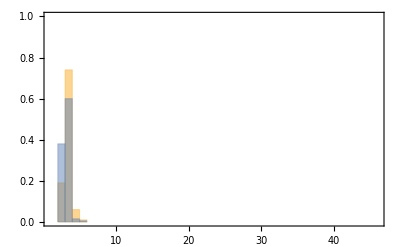
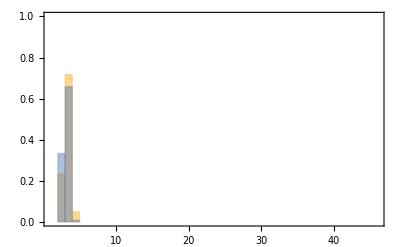
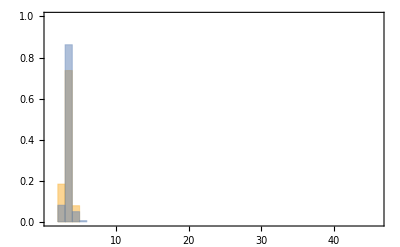
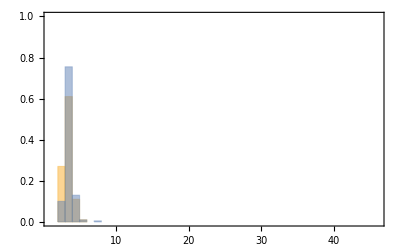
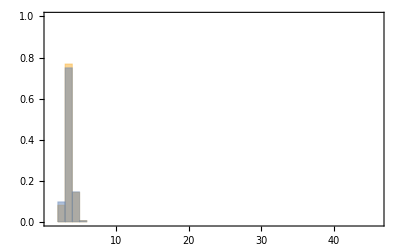
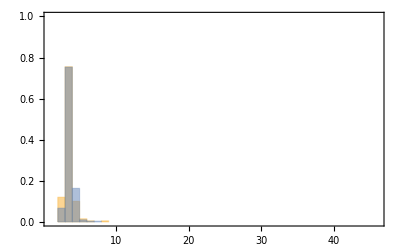
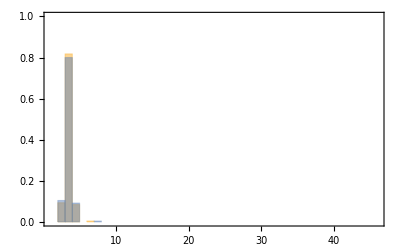
| FLASpring2021 | WestneckSummer2020 | FLASpring2020
WT | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-1 | -Graphics- | -Graphics- | N/A
Slclv3Pro-2 | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-3 | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-11 | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-12 | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-15 | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-18 | -Graphics- | -Graphics- | -Graphics-
Slclv3fas | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-22 | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-26 | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-28 | -Graphics- | -Graphics- | -Graphics-
Slclv3Pro-29 | -Graphics- | -Graphics- | -Graphics-

```mathematica
cle9histos=Table[
currentcounts={SelectFruits[{allele},{"WT"},{"WT"},{season}],
Select[data,#[[1]]==allele&&#[[2]]=="WT"&&#[[3]]=="Slcle9"&&((#[[5]]==season)||(season=="FLASpring2021"&&#[[5]]=="DoubleNullCompiled"))&][[All,4]]};
If[Length[currentcounts[[1]]]>0||Length[currentcounts[[2]]]>0,
Histogram[currentcounts,{Range[1,46]},"Probability",PlotRange->{{1,46},{0,1}},Frame->True],
"N/A"],
{allele,Part[CLV3alleles,allelicstrengthorder]},{season,{"FLASpring2021","WestneckSummer2020","FLASpring2020"}}];
Prepend[
Table[Prepend[cle9histos[[i]],CLV3alleles[[allelicstrengthorder[[i]]]]],{i,Length[CLV3alleles]}],
Join[{""},{"FLASpring2021","WestneckSummer2020","FLASpring2020"}]]//TableForm
```

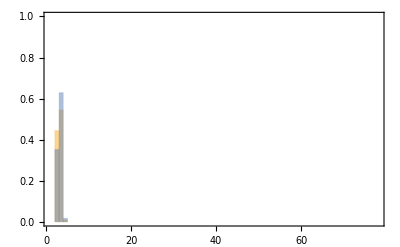
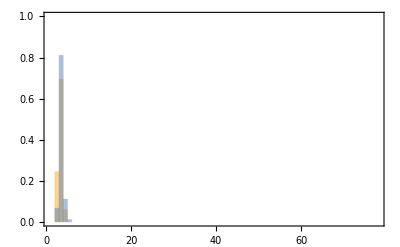
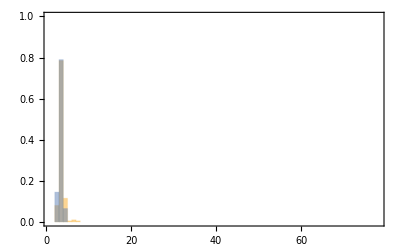
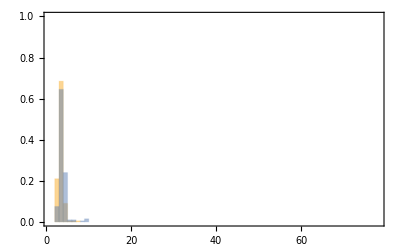
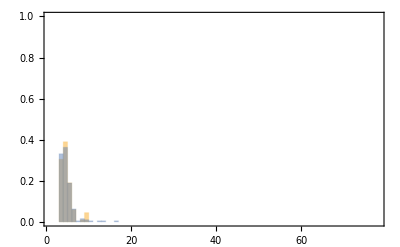
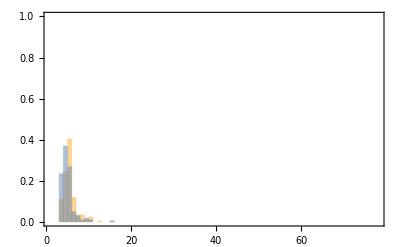
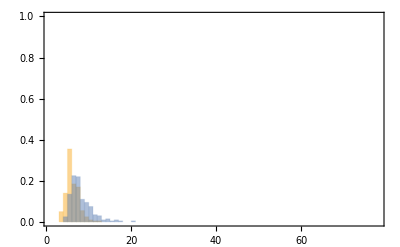
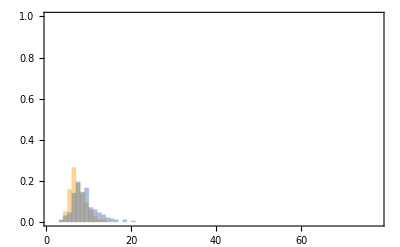
| WUS | SlwusCR-lc
WT | -Graphics- | -Graphics-
Slclv3Pro-2 | -Graphics- | -Graphics-
Slclv3Pro-11 | -Graphics- | -Graphics-
Slclv3fas | -Graphics- | -Graphics-
Slclv3Pro-22 | -Graphics- | -Graphics-
Slclv3Pro-26 | -Graphics- | -Graphics-
Slclv3Pro-29 | -Graphics- | -Graphics-

```mathematica
tripleshistos=Table[
currentcounts={
SelectFruits[{allele},{combo},{"WT"},{"FLASpring2022"}],
SelectFruits[{allele},{combo},{"Slcle9"},{"FLASpring2022"}]};
If[Length[currentcounts]>0,
Histogram[currentcounts,{Range[1,78]},"Probability",PlotRange->{{1,78},{0,1}},Frame->True],
"N/A"],
{allele,{"WT","Slclv3Pro-2","Slclv3Pro-11","Slclv3fas","Slclv3Pro-22","Slclv3Pro-26","Slclv3Pro-29"}},{combo,{"WT","SlwusCR-lc"}}];
Prepend[
Table[Prepend[tripleshistos[[i]],{"WT","Slclv3Pro-2","Slclv3Pro-11","Slclv3fas","Slclv3Pro-22","Slclv3Pro-26","Slclv3Pro-29"}[[i]]],{i,Length[tripleshistos]}],{"","WUS","SlwusCR-lc"}]//TableForm
```

## Main text analysis of epistatic hypotheses (Figures 1E, 2C, 3B)

### SlClv3^pro/CR-lc data

```mathematica
CLV3allelesByStrength=Most[Rest[CLV3alleles[[allelicstrengthorder]]]];
lcdata=Select[data,(#[[3]]=="WT"&&MemberQ[lcSeasons,#[[5]]]&&MemberQ[Join[{"WT"},CLV3allelesByStrength],#[[1]]])&];

lcdesignmatrix=
Table[
Join[
Table[If[lcdata[[i,1]]==CLV3allelesByStrength[[j]] ,1,0],{j,1,Length[CLV3allelesByStrength]}],
{If[lcdata[[i,2]]=="SlwusCR-lc",1,0]},
{N[Log[lcdata[[i,4]] ]]}
],
{i,Length[lcdata]}];
```

```mathematica
lcnoepistasis=NonlinearModelFit[lcdesignmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["SlwusCR-lc"] effect["SlwusCR-lc"] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["SlwusCR-lc"]}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"SlwusCR-lc"}]}]](*Variables*)
];
```

```mathematica
lcnoepistasis["ParameterTable"]
```

General::munfl: Exp[-4047.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-969.133] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1573.35] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.0517 | 0.00946965 | 111.06 | 0.
effect[Slclv3Pro-1] | -0.000660463 | 0.0125311 | -0.0527059 | 0.957967
effect[Slclv3Pro-2] | 0.0366896 | 0.0133485 | 2.74859 | 0.00599583
effect[Slclv3Pro-3] | 0.11432 | 0.0128911 | 8.86816 | 8.6797×10^-19
effect[Slclv3Pro-11] | 0.352451 | 0.0125311 | 28.1261 | 1.053×10^-167
effect[Slclv3Pro-12] | 0.357684 | 0.0125311 | 28.5437 | 1.79008×10^-172
effect[Slclv3Pro-15] | 0.467102 | 0.0122877 | 38.0139 | 7.68647×10^-296
effect[Slclv3Pro-18] | 0.566439 | 0.0122877 | 46.0982 | 0.
effect[Slclv3fas] | 0.746445 | 0.0123138 | 60.6186 | 0.
effect[Slclv3Pro-22] | 1.16184 | 0.0122762 | 94.6413 | 0.
effect[Slclv3Pro-26] | 1.38023 | 0.0122877 | 112.326 | 0.
effect[Slclv3Pro-28] | 1.71625 | 0.0170653 | 100.569 | 0.
effect[SlwusCR-lc] | 0.0761706 | 0.00513206 | 14.8421 | 2.55455×10^-49

```mathematica
lcconstantepistasis=NonlinearModelFit[lcdesignmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["SlwusCR-lc"] effect["SlwusCR-lc"]+x["SlwusCR-lc"]Table[x[i],{i,CLV3allelesByStrength}] .Table[epistasis,{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["SlwusCR-lc"]},{epistasis}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"SlwusCR-lc"}]}]](*Variables*)
];
```

```mathematica
lcconstantepistasis["ParameterTable"]
```

General::munfl: Exp[-2561.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1039.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2230.7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.05042 | 0.0128917 | 81.4804 | 0.
effect[Slclv3Pro-1] | 0.000740025 | 0.0157762 | 0.0469076 | 0.962588
effect[Slclv3Pro-2] | 0.0380622 | 0.0163223 | 2.33191 | 0.0197249
effect[Slclv3Pro-3] | 0.115708 | 0.0160139 | 7.22549 | 5.35022×10^-13
effect[Slclv3Pro-11] | 0.353852 | 0.0157762 | 22.4294 | 8.44705×10^-109
effect[Slclv3Pro-12] | 0.359085 | 0.0157762 | 22.7611 | 6.62247×10^-112
effect[Slclv3Pro-15] | 0.468501 | 0.0155793 | 30.0719 | 1.96134×10^-190
effect[Slclv3Pro-18] | 0.567839 | 0.0155793 | 36.4482 | 1.55045×10^-273
effect[Slclv3fas] | 0.747846 | 0.0156047 | 47.9244 | 0.
effect[Slclv3Pro-22] | 1.16323 | 0.0155682 | 74.7185 | 0.
effect[Slclv3Pro-26] | 1.38163 | 0.0155793 | 88.6832 | 0.
effect[Slclv3Pro-28] | 1.71766 | 0.0196243 | 87.5272 | 0.
effect[SlwusCR-lc] | 0.0787271 | 0.0182316 | 4.31817 | 0.0000158815
epistasis | -0.00277653 | 0.019 | -0.146133 | 0.883819

```mathematica
lcproportionalepistasis=NonlinearModelFit[lcdesignmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["SlwusCR-lc"] effect["SlwusCR-lc"]+x["SlwusCR-lc"]Table[x[i] effect[i],{i,CLV3allelesByStrength}] .Table[slope,{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["SlwusCR-lc"]},{slope}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"SlwusCR-lc"}]}]](*Variables*)
];
```

```mathematica
lcproportionalepistasis["ParameterTable"]
```

General::munfl: Exp[-3845.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-919.247] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1438.73] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.05456 | 0.00985161 | 107.045 | 0.
effect[Slclv3Pro-1] | -0.000356396 | 0.0124655 | -0.0285905 | 0.977192
effect[Slclv3Pro-2] | 0.0359933 | 0.0132956 | 2.70715 | 0.00679759
effect[Slclv3Pro-3] | 0.113683 | 0.0128373 | 8.85568 | 9.6998×10^-19
effect[Slclv3Pro-11] | 0.350665 | 0.0125851 | 27.8634 | 9.84662×10^-165
effect[Slclv3Pro-12] | 0.355698 | 0.0125893 | 28.2539 | 3.71149×10^-169
effect[Slclv3Pro-15] | 0.464513 | 0.0124603 | 37.2794 | 2.74883×10^-285
effect[Slclv3Pro-18] | 0.563629 | 0.0125869 | 44.779 | 0.
effect[Slclv3fas] | 0.742979 | 0.0129076 | 57.5615 | 0.
effect[Slclv3Pro-22] | 1.15486 | 0.0138175 | 83.5798 | 0.
effect[Slclv3Pro-26] | 1.37251 | 0.0144768 | 94.8078 | 0.
effect[Slclv3Pro-28] | 1.70591 | 0.0200135 | 85.2381 | 0.
effect[SlwusCR-lc] | 0.0704789 | 0.00766461 | 9.19536 | 4.46711×10^-20
slope | 0.0105858 | 0.0106571 | 0.993312 | 0.320582

```mathematica
lcidiosyncraticepistasis=NonlinearModelFit[lcdesignmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["SlwusCR-lc"] effect["SlwusCR-lc"]+x["SlwusCR-lc"]Table[x[i],{i,CLV3allelesByStrength}].Table[epistasis[i],{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["SlwusCR-lc"]},Table[epistasis[i],{i,CLV3allelesByStrength}]](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"SlwusCR-lc"}]}]](*Variables*)
];
```

```mathematica
lcidiosyncraticepistasis["ParameterTable"]
```

General::munfl: Exp[-2643.14] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2139.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2419.95] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.05042 | 0.0126328 | 83.1499 | 0.
effect[Slclv3Pro-1] | 0.00218303 | 0.0178655 | 0.122192 | 0.902749
effect[Slclv3Pro-2] | 0.0576348 | 0.0178655 | 3.22603 | 0.00125915
effect[Slclv3Pro-3] | 0.120381 | 0.0178655 | 6.73819 | 1.69033×10^-11
effect[Slclv3Pro-11] | 0.35891 | 0.0178655 | 20.0895 | 4.55908×10^-88
effect[Slclv3Pro-12] | 0.400325 | 0.0178655 | 22.4077 | 1.35331×10^-108
effect[Slclv3Pro-15] | 0.500035 | 0.0174548 | 28.6475 | 1.16244×10^-173
effect[Slclv3Pro-18] | 0.523283 | 0.0174548 | 29.9793 | 2.57478×10^-189
effect[Slclv3fas] | 0.615975 | 0.0175413 | 35.1156 | 4.13475×10^-255
effect[Slclv3Pro-22] | 1.26865 | 0.0174173 | 72.8383 | 0.
effect[Slclv3Pro-26] | 1.37228 | 0.0174548 | 78.619 | 0.
effect[Slclv3Pro-28] | 1.64334 | 0.0262973 | 62.4909 | 0.
effect[SlwusCR-lc] | 0.0787271 | 0.0178655 | 4.40665 | 0.0000106057
epistasis[Slclv3Pro-1] | -0.00537394 | 0.0246259 | -0.218223 | 0.82726
epistasis[Slclv3Pro-2] | -0.048446 | 0.0262973 | -1.84224 | 0.0654691
epistasis[Slclv3Pro-3] | -0.0121229 | 0.0252657 | -0.479816 | 0.631369
epistasis[Slclv3Pro-11] | -0.0118814 | 0.0246259 | -0.482477 | 0.629478
epistasis[Slclv3Pro-12] | -0.0770097 | 0.0246259 | -3.12718 | 0.0017699
epistasis[Slclv3Pro-15] | -0.060005 | 0.0241344 | -2.48628 | 0.0129245
epistasis[Slclv3Pro-18] | 0.0780846 | 0.0241344 | 3.2354 | 0.00121861
epistasis[Slclv3fas] | 0.234347 | 0.0241971 | 9.68489 | 4.35187×10^-22
epistasis[Slclv3Pro-22] | -0.19486 | 0.0241074 | -8.08302 | 7.03482×10^-16
epistasis[Slclv3Pro-26] | 0.0141911 | 0.0241344 | 0.588001 | 0.556545
epistasis[Slclv3Pro-28] | 0.116132 | 0.0342099 | 3.3947 | 0.000689651

### ModelComparison

These are all likelihood ratio tests.

p-value for constant epistasis vs. no epistasis

```mathematica
1-CDF[ChiSquareDistribution[1],2(ResidualsToLogLikelihood[lcconstantepistasis["FitResiduals"]]-ResidualsToLogLikelihood[lcnoepistasis["FitResiduals"]])]
```

0.883737

p-value for  proportional epistasis vs. no epistasis

```mathematica
1-CDF[ChiSquareDistribution[1],2(ResidualsToLogLikelihood[lcproportionalepistasis["FitResiduals"]]-ResidualsToLogLikelihood[lcnoepistasis["FitResiduals"]])]
```

0.319848

p-value for idiosyncratic epistasis vs. no epistasis

```mathematica
1-CDF[ChiSquareDistribution[11],2(ResidualsToLogLikelihood[lcidiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[lcnoepistasis["FitResiduals"]])]
```

0.

2 * difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[lcidiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[lcnoepistasis["FitResiduals"]])
```

424.405

p-value for idiosyncratic epistasis vs. constant epistasis

```mathematica
1-CDF[ChiSquareDistribution[10],2(ResidualsToLogLikelihood[lcidiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[lcconstantepistasis["FitResiduals"]])]
```

0.

2 * difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[lcidiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[lcconstantepistasis["FitResiduals"]])
```

424.383

p-value for idiosyncratic epistasis vs. proportional epistasis

```mathematica
1-CDF[ChiSquareDistribution[10],2(ResidualsToLogLikelihood[lcidiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[lcproportionalepistasis["FitResiduals"]])]
```

0.

2 * difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[lcidiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[lcproportionalepistasis["FitResiduals"]])
```

423.415

```mathematica
Prepend[SortBy[Table[ {model,ResidualsToLogLikelihood[ToExpression[model]["FitResiduals"]]},{model,{"lcnoepistasis","lcconstantepistasis","lcproportionalepistasis","lcidiosyncraticepistasis"}}],Last]//Reverse,{"Model","Log Likelihood"}]//TableForm
```

Model | Log Likelihood
lcidiosyncraticepistasis | -429.429
lcproportionalepistasis | -641.136
lcconstantepistasis | -641.62
lcnoepistasis | -641.631

### Figure 1E

Code to make Figure 1E

```mathematica
wuslogseffect=Table[
currentcounts={SelectFruits[{allele},{"WT"},{"WT"},{season}],SelectFruits[{allele},{"SlwusCR-lc"},{"WT"},{season}]};
{If[Length[currentcounts[[1]]]>0,N[MeanAround[Log[currentcounts[[1]]]]],"N/A"],If[Length[currentcounts[[2]]]>0&&Length[currentcounts[[1]]]>0,N[MeanAround[Log[currentcounts[[2]]]]]-MeanAround[Log[currentcounts[[1]]]],"N/A"]},
{allele,Join[{"WT"},CLV3allelesByStrength]},{season,lcSeasons}]
```

{{{1.0550.014,0.0630.021},{1.0460.013,0.0940.019}},{{1.0130.016,0.1110.020},{1.0920.014,0.0360.020}},{{1.0820.014,0.0740.028},{1.1340.013,-0.0040.020}},{{1.1700.013,0.1070.021},{1.1710.014,0.0260.022}},{{1.4390.019,0.0090.026},{1.3790.017,0.1380.025}},{{1.4370.018,-0.0110.023},{1.4640.017,0.0280.026}},{{1.5530.021,0.0240.027},{1.5490.019,0.0110.026}},{{1.6290.017,0.0880.023},{1.5280.023,0.2200.029}},{{1.6400.025,0.3450.030},{1.6870.016,0.2850.026}},{{2.2840.019,-0.0940.024},{2.3480.016,-0.1290.022}},{{2.4530.020,0.0940.025},{2.3980.011,0.0790.017}},{{2.6940.016,0.1950.023},{N/A,N/A}}}

```mathematica
lcplotlabels={"WT",1,2,3,11,12,15,18,"fas",22,26,28}
pointstoplot=Transpose[wuslogseffect];
pointstoplot1=Select[pointstoplot[[1]],!(#[[1]]==="N/A"||#[[2]]==="N/A")&]
pointstoplot2=Select[pointstoplot[[2]],!(#[[1]]==="N/A"||#[[2]]==="N/A")&]
Show[ListPlot[{pointstoplot1->lcplotlabels,pointstoplot2->Most[lcplotlabels] (*Note this season is missing allele 28 and so has one fewer point plotted, hence the "Most" around its labels*)},PlotStyle->PointSize[Medium],PlotLegends->PointLegend[Automatic,lcSeasons],Frame->True,FrameStyle->AbsoluteThickness[1],FrameTicksStyle->AbsoluteThickness[1],FrameLabel->{"Locule number, WUS background","CR-lc effect "},PlotRangePadding->False,AspectRatio->Automatic,LabelStyle->Medium,PlotRange->{{Log[2.5],Log[14]},{Log[.8],Log[1.6]}},FrameTicks->{
{Transpose[{Log[Range[.8,1.6,.1]],{"-20 %","","+0%","","+20 %","","+40 %","","+60 %"}}],None},{Transpose[{N[Log[Join[Range[1,16]]]],Join[Range[1,16]]}],None}},ImageSize->8 72],
Plot[Mean[wuslogseffect[[1,All,2,1]]],{x,Log[2.5],Log[17]},PlotStyle->{Gray,Dashed,AbsoluteThickness[2]}]]
(*Note that the coloring scheme is reversed in the main text figure (WestneckSummer2021 is yellow in the main text figure and FLAFall2021 is blue)*)
```

{WT,1,2,3,11,12,15,18,fas,22,26,28}

{{1.0550.014,0.0630.021},{1.0130.016,0.1110.020},{1.0820.014,0.0740.028},{1.1700.013,0.1070.021},{1.4390.019,0.0090.026},{1.4370.018,-0.0110.023},{1.5530.021,0.0240.027},{1.6290.017,0.0880.023},{1.6400.025,0.3450.030},{2.2840.019,-0.0940.024},{2.4530.020,0.0940.025},{2.6940.016,0.1950.023}}

{{1.0460.013,0.0940.019},{1.0920.014,0.0360.020},{1.1340.013,-0.0040.020},{1.1710.014,0.0260.022},{1.3790.017,0.1380.025},{1.4640.017,0.0280.026},{1.5490.019,0.0110.026},{1.5280.023,0.2200.029},{1.6870.016,0.2850.026},{2.3480.016,-0.1290.022},{2.3980.011,0.0790.017}}

-Graphics-

### SlClv3^pro/Slcle9 data

```mathematica
CLV3allelesByStrength=Most[Rest[CLV3alleles[[allelicstrengthorder]]]];
cle9data=Select[data,(#[[2]]=="WT"&&MemberQ[cle9Seasons,#[[5]]]&&MemberQ[Join[{"WT"},CLV3allelesByStrength],#[[1]]])&];

cle9designmatrix=
Table[
Join[
Table[If[cle9data[[i,1]]==CLV3allelesByStrength[[j]] ,1,0],{j,1,Length[CLV3allelesByStrength]}],
{If[cle9data[[i,3]]=="Slcle9",1,0]},
{N[Log[cle9data[[i,4]] ]]}
],
{i,Length[cle9data]}];
```

```mathematica
cle9noepistasis=NonlinearModelFit[cle9designmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["cle9"] effect["cle9"] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["cle9"]}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"cle9"}]}]](*Variables*)
];
```

```mathematica
cle9noepistasis["ParameterTable"]
```

General::munfl: Exp[-4137.36] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1030.42] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1745.88] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 0.945766 | 0.008924 | 105.98 | 0.
effect[Slclv3Pro-1] | 0.0694302 | 0.0126642 | 5.48239 | 4.26811×10^-8
effect[Slclv3Pro-2] | 0.104922 | 0.0109237 | 9.60503 | 8.87383×10^-22
effect[Slclv3Pro-3] | 0.12808 | 0.0110782 | 11.5614 | 8.88985×10^-31
effect[Slclv3Pro-11] | 0.375219 | 0.0106576 | 35.2066 | 2.3672×10^-260
effect[Slclv3Pro-12] | 0.410155 | 0.0107593 | 38.1211 | 9.3592×10^-303
effect[Slclv3Pro-15] | 0.501701 | 0.0106735 | 47.0045 | 0.
effect[Slclv3Pro-18] | 0.662395 | 0.0105393 | 62.8499 | 0.
effect[Slclv3fas] | 0.768214 | 0.0119064 | 64.5212 | 0.
effect[Slclv3Pro-22] | 1.17314 | 0.010744 | 109.19 | 0.
effect[Slclv3Pro-26] | 1.45647 | 0.0107559 | 135.412 | 0.
effect[Slclv3Pro-28] | 1.65175 | 0.0132059 | 125.077 | 0.
effect[cle9] | 0.0959243 | 0.00408093 | 23.5055 | 7.05399×10^-120

```mathematica
cle9constantepistasis=NonlinearModelFit[cle9designmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["cle9"] effect["cle9"]+x["cle9"]Table[x[i],{i,CLV3allelesByStrength}] .Table[epistasis,{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["cle9"]},{epistasis}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"cle9"}]}]](*Variables*)
];
```

```mathematica
cle9constantepistasis["ParameterTable"]
```

General::munfl: Exp[-2633.65] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-721.114] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-874.377] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.03883 | 0.0130155 | 79.8148 | 0.
effect[Slclv3Pro-1] | -0.0287695 | 0.01612 | -1.78471 | 0.074329
effect[Slclv3Pro-2] | 0.00660689 | 0.0148091 | 0.446138 | 0.655504
effect[Slclv3Pro-3] | 0.0302081 | 0.0148922 | 2.02846 | 0.0425325
effect[Slclv3Pro-11] | 0.277347 | 0.0145841 | 19.0171 | 1.21408×10^-79
effect[Slclv3Pro-12] | 0.312115 | 0.0146698 | 21.2761 | 6.68589×10^-99
effect[Slclv3Pro-15] | 0.403787 | 0.0145986 | 27.6593 | 4.86065×10^-164
effect[Slclv3Pro-18] | 0.564216 | 0.0145201 | 38.8575 | 6.67015×10^-314
effect[Slclv3fas] | 0.669671 | 0.0155583 | 43.0428 | 0.
effect[Slclv3Pro-22] | 1.07546 | 0.0146335 | 73.4931 | 0.
effect[Slclv3Pro-26] | 1.35917 | 0.0146155 | 92.9949 | 0.
effect[Slclv3Pro-28] | 1.55626 | 0.0163802 | 95.0085 | 0.
effect[cle9] | -0.0690504 | 0.0173293 | -3.9846 | 0.0000679323
epistasis | 0.174593 | 0.0178273 | 9.79355 | 1.41588×10^-22

```mathematica
cle9proportionalepistasis=NonlinearModelFit[cle9designmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["cle9"] effect["cle9"]+x["cle9"]Table[x[i] effect[i],{i,CLV3allelesByStrength}] .Table[slope,{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["cle9"]},{slope}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"cle9"}]}]](*Variables*)
];
```

```mathematica
cle9proportionalepistasis["ParameterTable"]
```

General::munfl: Exp[-5306.33] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1020.02] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1684.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.025 | 0.00815573 | 125.678 | 0.
effect[Slclv3Pro-1] | 0.0627215 | 0.0106316 | 5.89954 | 3.72862×10^-9
effect[Slclv3Pro-2] | 0.0919364 | 0.00916006 | 10.0367 | 1.26194×10^-23
effect[Slclv3Pro-3] | 0.103521 | 0.00934503 | 11.0776 | 2.10825×10^-28
effect[Slclv3Pro-11] | 0.319422 | 0.00914842 | 34.9156 | 2.85082×10^-256
effect[Slclv3Pro-12] | 0.351781 | 0.00925032 | 38.029 | 2.25817×10^-301
effect[Slclv3Pro-15] | 0.434588 | 0.00929633 | 46.7483 | 0.
effect[Slclv3Pro-18] | 0.578837 | 0.00939762 | 61.594 | 0.
effect[Slclv3fas] | 0.671713 | 0.010629 | 63.1965 | 0.
effect[Slclv3Pro-22] | 1.02996 | 0.010547 | 97.6535 | 0.
effect[Slclv3Pro-26] | 1.2808 | 0.0111284 | 115.093 | 0.
effect[Slclv3Pro-28] | 1.50734 | 0.0129339 | 116.542 | 0.
effect[cle9] | -0.0468241 | 0.00644972 | -7.25985 | 4.07731×10^-13
slope | 0.273106 | 0.0104984 | 26.0139 | 9.0659×10^-146

```mathematica
cle9idiosyncraticepistasis=NonlinearModelFit[cle9designmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["cle9"] effect["cle9"]+x["cle9"]Table[x[i],{i,CLV3allelesByStrength}].Table[epistasis[i],{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["cle9"]},Table[epistasis[i],{i,CLV3allelesByStrength}]](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"cle9"}]}]](*Variables*)
];
```

```mathematica
cle9idiosyncraticepistasis["ParameterTable"]
```

General::munfl: Exp[-2787.76] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1869.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3044.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.03883 | 0.012576 | 82.6041 | 0.
effect[Slclv3Pro-1] | -0.00540804 | 0.0181496 | -0.29797 | 0.76573
effect[Slclv3Pro-2] | 0.0576119 | 0.0158138 | 3.64315 | 0.000270284
effect[Slclv3Pro-3] | 0.113609 | 0.0157409 | 7.21744 | 5.56761×10^-13
effect[Slclv3Pro-11] | 0.345877 | 0.0151928 | 22.7658 | 1.05681×10^-112
effect[Slclv3Pro-12] | 0.369798 | 0.0154176 | 23.9855 | 1.20711×10^-124
effect[Slclv3Pro-15] | 0.42093 | 0.0152355 | 27.6282 | 1.10586×10^-163
effect[Slclv3Pro-18] | 0.526843 | 0.0151961 | 34.6697 | 7.69866×10^-253
effect[Slclv3fas] | 0.593733 | 0.0174209 | 34.0816 | 9.88169×10^-245
effect[Slclv3Pro-22] | 0.993461 | 0.0152058 | 65.3343 | 0.
effect[Slclv3Pro-26] | 1.3112 | 0.0150407 | 87.1771 | 0.
effect[Slclv3Pro-28] | 1.47575 | 0.0167442 | 88.1354 | 0.
effect[cle9] | -0.0690504 | 0.0167442 | -4.12385 | 0.0000374718
epistasis[Slclv3Pro-1] | 0.130855 | 0.024515 | 5.33773 | 9.55737×10^-8
epistasis[Slclv3Pro-2] | 0.081204 | 0.0211818 | 3.83367 | 0.000126792
epistasis[Slclv3Pro-3] | 0.00779017 | 0.0214385 | 0.363373 | 0.716332
epistasis[Slclv3Pro-11] | 0.0375321 | 0.0206325 | 1.81908 | 0.0689203
epistasis[Slclv3Pro-12] | 0.0631255 | 0.0208346 | 3.02984 | 0.00245129
epistasis[Slclv3Pro-15] | 0.140607 | 0.0206639 | 6.80445 | 1.05522×10^-11
epistasis[Slclv3Pro-18] | 0.244844 | 0.0204242 | 11.988 | 5.93797×10^-33
epistasis[Slclv3fas] | 0.307871 | 0.0231396 | 13.305 | 3.77757×10^-40
epistasis[Slclv3Pro-22] | 0.345474 | 0.0207996 | 16.6097 | 2.2657×10^-61
epistasis[Slclv3Pro-26] | 0.283581 | 0.0208572 | 13.5963 | 7.72571×10^-42
epistasis[Slclv3Pro-28] | 0.492836 | 0.027631 | 17.8364 | 2.17958×10^-70

### ModelComparison

These are all likelihood ratio tests.

p-value for constant epistasis vs. no epistasis

```mathematica
1-CDF[ChiSquareDistribution[1],2(ResidualsToLogLikelihood[ cle9constantepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9noepistasis["FitResiduals"]])]
```

0.

2 * difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[ cle9constantepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9noepistasis["FitResiduals"]])
```

95.6843

p-value for  proportional epistasis vs. constant epistasis

```mathematica
1-CDF[ChiSquareDistribution[1],2(ResidualsToLogLikelihood[cle9proportionalepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9constantepistasis["FitResiduals"]])]
```

0.

2 * difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[cle9proportionalepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9constantepistasis["FitResiduals"]])
```

739.047

p-value for idiosyncratic epistasis vs. proportional epistasis

```mathematica
1-CDF[ChiSquareDistribution[10],2(ResidualsToLogLikelihood[cle9idiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9proportionalepistasis["FitResiduals"]])]
```

0.

2 * difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[cle9idiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9proportionalepistasis["FitResiduals"]])
```

242.737

#### Sigmoid epistasis model

```mathematica
cle9sigmoidepistasis=NonlinearModelFit[cle9designmatrix,
wt +Table[x[i],{i,CLV3allelesByStrength}].Table[effect[i],{i,CLV3allelesByStrength}]+x["CR-cle9"] effect["CR-cle9"]+x["CR-cle9"]Table[x[i],{i,CLV3allelesByStrength}].Table[
a 1/(1+ⅇ^(-m Table[x[i],{i,CLV3allelesByStrength}].Table[effect[i],{i,CLV3allelesByStrength}]+b))+c
,{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["CR-cle9"]},{a,b,m,c}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"CR-cle9"}]}]](*Variables*)
];
```

```mathematica
cle9sigmoidepistasis["ParameterTable"]
```

General::munfl: Exp[-2771.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-717.434] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2025.54] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.03883 | 0.0126226 | 82.2989 | 0.
effect[Slclv3Pro-1] | 0.0357624 | 0.016005 | 2.23444 | 0.0254695
effect[Slclv3Pro-2] | 0.0725829 | 0.0147816 | 4.91035 | 9.19297×10^-7
effect[Slclv3Pro-3] | 0.090586 | 0.0147912 | 6.12433 | 9.34808×10^-10
effect[Slclv3Pro-11] | 0.332113 | 0.0141497 | 23.4715 | 1.52697×10^-119
effect[Slclv3Pro-12] | 0.364616 | 0.0142512 | 25.5849 | 3.59719×10^-141
effect[Slclv3Pro-15] | 0.433693 | 0.0144648 | 29.9826 | 1.55263×10^-191
effect[Slclv3Pro-18] | 0.52227 | 0.0146091 | 35.7496 | 4.87904×10^-268
effect[Slclv3fas] | 0.590411 | 0.0152353 | 38.7528 | 2.64537×10^-312
effect[Slclv3Pro-22] | 0.997162 | 0.0145759 | 68.4115 | 0.
effect[Slclv3Pro-26] | 1.28736 | 0.0144989 | 88.7901 | 0.
effect[Slclv3Pro-28] | 1.51498 | 0.0159823 | 94.7915 | 0.
effect[CR-cle9] | -0.0690504 | 0.0168063 | -4.10861 | 0.0000400284
a | -0.283991 | 0.0113064 | -25.1178 | 3.03872×10^-136
b | -10.817 | 2.15622 | -5.01665 | 5.32182×10^-7
m | -22.2881 | 4.37488 | -5.09456 | 3.5406×10^-7
c | 0.337763 | 0.0186266 | 18.1333 | 1.15752×10^-72

Likelihood ratio test versus the idiosyncratic epistasis model

```mathematica
1-CDF[ChiSquareDistribution[7],2(ResidualsToLogLikelihood[cle9idiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9sigmoidepistasis["FitResiduals"]])]
```

0.

2*difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[cle9idiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9sigmoidepistasis["FitResiduals"]])
```

111.742

Likelihood ratio test versus proportional epistasis

```mathematica
1-CDF[ChiSquareDistribution[3],2(ResidualsToLogLikelihood[cle9sigmoidepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9proportionalepistasis["FitResiduals"]])]
```

0.

2*difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[cle9sigmoidepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9proportionalepistasis["FitResiduals"]])
```

130.995

Comparison with constant epistasis model (similar to extrapolation behavior of idiosyncratic epistasis)

```mathematica
2(ResidualsToLogLikelihood[cle9sigmoidepistasis["FitResiduals"]]-ResidualsToLogLikelihood[cle9constantepistasis["FitResiduals"]])
```

870.042

```mathematica
Prepend[SortBy[Table[ {model,ResidualsToLogLikelihood[ToExpression[model]["FitResiduals"]]},{model,{"cle9noepistasis","cle9constantepistasis","cle9proportionalepistasis","cle9idiosyncraticepistasis","cle9sigmoidepistasis"}}],Last]//Reverse,{"Model","Log Likelihood"}]//TableForm
```

Model | Log Likelihood
cle9idiosyncraticepistasis | 613.941
cle9sigmoidepistasis | 558.07
cle9proportionalepistasis | 492.572
cle9constantepistasis | 123.049
cle9noepistasis | 75.2065

### Figure 2C

```mathematica
cle9logseffect=Table[
currentcounts={Select[cle9data,#[[1]]==allele&&#[[2]]=="WT"&&#[[3]]=="WT"&&#[[5]]==season&][[All,4]],Select[cle9data,#[[1]]==allele&&#[[3]]=="Slcle9"&&#[[2]]=="WT"&&#[[5]]==season&][[All,4]]};
{If[Length[currentcounts[[1]]]>0,N[MeanAround[Log[currentcounts[[1]]]]],"N/A"],If[Length[currentcounts[[2]]]>0&&Length[currentcounts[[1]]]>0,N[MeanAround[Log[currentcounts[[2]]]]]-MeanAround[Log[currentcounts[[1]]]],"N/A"]},
{allele,Join[{"WT"},CLV3allelesByStrength]},{season,cle9Seasons}]
```

{{{1.0550.016,-0.0510.026},{1.0440.019,-0.0930.024},{1.0180.017,-0.0530.025}},{{1.0470.017,0.0370.021},{1.0260.016,0.0790.021},{N/A,N/A}},{{1.1100.013,-0.0060.019},{1.0950.014,0.0340.017},{1.0880.010,-0.0020.015}},{{1.1300.014,-0.0140.021},{1.1730.011,-0.0450.017},{1.1500.010,-0.1060.016}},{{1.3780.013,-0.0520.018},{1.4130.014,-0.0760.022},{1.3710.014,0.0140.019}},{{1.3870.013,0.0010.018},{1.4350.016,-0.0130.023},{1.4080.015,-0.0070.022}},{{1.3710.013,0.1120.020},{1.5410.019,0.0490.027},{1.4770.016,0.0540.022}},{{1.4810.014,0.1710.020},{1.6030.016,0.1680.021},{1.6090.013,0.1740.022}},{{1.5900.016,0.2210.022},{1.6570.035,0.230.05},{1.6510.024,0.3110.034}},{{1.9880.017,0.2950.024},{2.1070.018,0.2530.024},{2.0180.015,0.2240.027}},{{2.3260.016,0.2420.019},{2.4110.014,0.1580.020},{2.2990.015,0.2430.025}},{{2.6940.016,0.1760.028},{2.5220.019,0.4540.035},{2.3230.029,N/A}}}

```mathematica
cle9plotlabels={"WT",1,2,3,11,12,15,18,"fas",22,26,28}
pointstoplot=Transpose[cle9logseffect];
pointstoplot1=Select[pointstoplot[[1]],!(#[[1]]==="N/A"||#[[2]]==="N/A")&]
pointstoplot2=Select[pointstoplot[[2]],!(#[[1]]==="N/A"||#[[2]]==="N/A")&]
pointstoplot3=Select[pointstoplot[[3]],!(#[[1]]==="N/A"||#[[2]]==="N/A")&]
Show[ListPlot[{
pointstoplot1->cle9plotlabels,
pointstoplot2->cle9plotlabels,
pointstoplot3->Most[Drop[cle9plotlabels,{2}]](*Note this season is missing alleles 1 and 28 and so has two fewer points plotted*)},PlotStyle->PointSize[Medium],PlotLegends->PointLegend[Automatic,cle9Seasons],Frame->True,FrameStyle->AbsoluteThickness[1],FrameTicksStyle->AbsoluteThickness[1],FrameLabel->{"Locule number, WUS background","CR-cle9 effect "},PlotRangePadding->False,AspectRatio->Automatic,LabelStyle->Medium,PlotRange->{{Log[2.5],Log[14]},{Log[.8],Log[1.6]}},FrameTicks->{
{Transpose[{Log[Range[.8,1.7,.1]],{"-20 %","","+0%","","+20 %","","+40 %","","+60 %",""}}],None},{Transpose[{N[Log[Join[Range[1,16]]]],Join[Range[1,16]]}],None}},ImageSize->8 72],
Plot[effect["CR-cle9"] +a 1/(1+ⅇ^(-m (x-wt)+b))+c/.cle9sigmoidepistasis["BestFitParameters"],{x,Log[2.5],Log[16.25]},PlotStyle->{Black,AbsoluteThickness[2]}]]
```

{WT,1,2,3,11,12,15,18,fas,22,26,28}

{{1.0550.016,-0.0510.026},{1.0470.017,0.0370.021},{1.1100.013,-0.0060.019},{1.1300.014,-0.0140.021},{1.3780.013,-0.0520.018},{1.3870.013,0.0010.018},{1.3710.013,0.1120.020},{1.4810.014,0.1710.020},{1.5900.016,0.2210.022},{1.9880.017,0.2950.024},{2.3260.016,0.2420.019},{2.6940.016,0.1760.028}}

{{1.0440.019,-0.0930.024},{1.0260.016,0.0790.021},{1.0950.014,0.0340.017},{1.1730.011,-0.0450.017},{1.4130.014,-0.0760.022},{1.4350.016,-0.0130.023},{1.5410.019,0.0490.027},{1.6030.016,0.1680.021},{1.6570.035,0.230.05},{2.1070.018,0.2530.024},{2.4110.014,0.1580.020},{2.5220.019,0.4540.035}}

{{1.0180.017,-0.0530.025},{1.0880.010,-0.0020.015},{1.1500.010,-0.1060.016},{1.3710.014,0.0140.019},{1.4080.015,-0.0070.022},{1.4770.016,0.0540.022},{1.6090.013,0.1740.022},{1.6510.024,0.3110.034},{2.0180.015,0.2240.027},{2.2990.015,0.2430.025}}

-Graphics-

### Triple mutants

```mathematica
CLV3allelesByStrength={"Slclv3Pro-2","Slclv3Pro-11","Slclv3fas","Slclv3Pro-22","Slclv3Pro-26"};
triplesdata=Select[data,(#[[2]]=="SlwusCR-lc"&&#[[5]]=="FLASpring2022"&&MemberQ[Join[{"WT"},CLV3allelesByStrength],#[[1]]])&];

triplesdesignmatrix=
Table[
Join[
Table[If[triplesdata[[i,1]]==CLV3allelesByStrength[[j]] ,1,0],{j,1,Length[CLV3allelesByStrength]}],
{If[triplesdata[[i,3]]=="Slcle9",1,0]},
{N[Log[triplesdata[[i,4]] ]]}
],
{i,Length[triplesdata]}];
```

Note that in the analyses below, the parameter “wt” is the estimated log locule number of the CR-lc single mutant, and we are conducting a double-mutant epistasis analysis in this single mutant background. Underflows due to very small p-values.

```mathematica
triplesnoepistasis=NonlinearModelFit[triplesdesignmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["cle9"] effect["cle9"] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["cle9"]}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"cle9"}]}]](*Variables*)
];
```

```mathematica
triplesnoepistasis["ParameterTable"]
```

General::munfl: Exp[-1176.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.457] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1174.42] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.00623 | 0.01572 | 64.0095 | 0.
effect[Slclv3Pro-2] | 0.0409655 | 0.0202594 | 2.02205 | 0.0432876
effect[Slclv3Pro-11] | 0.450634 | 0.0202594 | 22.2433 | 2.33649×10^-99
effect[Slclv3fas] | 0.928524 | 0.0203077 | 45.7228 | 0.
effect[Slclv3Pro-22] | 1.29519 | 0.0202594 | 63.9305 | 0.
effect[Slclv3Pro-26] | 1.58674 | 0.0202594 | 78.3215 | 0.
effect[cle9] | 0.125891 | 0.0110306 | 11.4129 | 2.2257×10^-29

```mathematica
triplesconstantepistasis=NonlinearModelFit[triplesdesignmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["cle9"] effect["cle9"]+x["cle9"]Table[x[i],{i,CLV3allelesByStrength}] .Table[epistasis,{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["cle9"]},{epistasis}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"cle9"}]}]](*Variables*)
];
```

```mathematica
triplesconstantepistasis["ParameterTable"]
```

General::munfl: Exp[-966.789] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-963.669] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1252.25] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.01653 | 0.0184746 | 55.0233 | 0.
effect[Slclv3Pro-2] | 0.0285957 | 0.0233702 | 1.2236 | 0.22123
effect[Slclv3Pro-11] | 0.438265 | 0.0233702 | 18.7531 | 4.39565×10^-73
effect[Slclv3fas] | 0.916133 | 0.0234219 | 39.1144 | 1.85764×10^-256
effect[Slclv3Pro-22] | 1.28282 | 0.0233702 | 54.8913 | 0.
effect[Slclv3Pro-26] | 1.57437 | 0.0233702 | 67.3667 | 0.
effect[cle9] | 0.0926875 | 0.0331629 | 2.79491 | 0.00523483
epistasis | 0.037334 | 0.035165 | 1.06168 | 0.288494

```mathematica
triplesproportionalepistasis=NonlinearModelFit[triplesdesignmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["cle9"] effect["cle9"]+x["cle9"]Table[x[i] effect[i],{i,CLV3allelesByStrength}] .Table[slope,{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["cle9"]},{slope}](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"cle9"}]}]](*Variables*)
];
```

```mathematica
triplesproportionalepistasis["ParameterTable"]
```

General::munfl: Exp[-1226.92] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1013.06] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1203.66] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.04231 | 0.0157343 | 66.2448 | 0.
effect[Slclv3Pro-2] | 0.0582332 | 0.0189754 | 3.06887 | 0.00217399
effect[Slclv3Pro-11] | 0.429363 | 0.0189644 | 22.6405 | 1.56927×10^-102
effect[Slclv3fas] | 0.881877 | 0.0200352 | 44.0164 | 8.89919×10^-307
effect[Slclv3Pro-22] | 1.22105 | 0.0214269 | 56.9867 | 0.
effect[Slclv3Pro-26] | 1.49482 | 0.0229196 | 65.2202 | 0.
effect[cle9] | 0.0170971 | 0.0183991 | 0.929234 | 0.352866
slope | 0.150045 | 0.0210864 | 7.11571 | 1.48522×10^-12

```mathematica
triplesidiosyncraticepistasis=NonlinearModelFit[triplesdesignmatrix,
wt +Table[x[i],{i,Join[CLV3allelesByStrength]}].Join[Table[effect[i],{i,CLV3allelesByStrength}]]+x["cle9"] effect["cle9"]+x["cle9"]Table[x[i],{i,CLV3allelesByStrength}].Table[epistasis[i],{i,CLV3allelesByStrength}] (*Model*),
Join[{wt},Table[effect[i],{i,CLV3allelesByStrength}],{effect["cle9"]},Table[epistasis[i],{i,CLV3allelesByStrength}]](*Parameters*),
Join[Table[x[i],{i,Join[CLV3allelesByStrength,{"cle9"}]}]](*Variables*)
];
```

```mathematica
triplesidiosyncraticepistasis["ParameterTable"]
```

General::munfl: Exp[-1009.09] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-842.583] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1058.81] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
wt | 1.01653 | 0.0178832 | 56.8431 | 0.
effect[Slclv3Pro-2] | 0.0330781 | 0.0252906 | 1.30792 | 0.191033
effect[Slclv3Pro-11] | 0.568164 | 0.0252906 | 22.4654 | 4.13925×10^-101
effect[Slclv3fas] | 0.887225 | 0.0254193 | 34.9036 | 4.07866×10^-214
effect[Slclv3Pro-22] | 1.25982 | 0.0252906 | 49.8139 | 0.
effect[Slclv3Pro-26] | 1.49132 | 0.0252906 | 58.9672 | 0.
effect[cle9] | 0.0926875 | 0.0321013 | 2.88735 | 0.00392174
epistasis[Slclv3Pro-2] | 0.0283693 | 0.0408669 | 0.694186 | 0.487636
epistasis[Slclv3Pro-11] | -0.222464 | 0.0408669 | -5.44362 | 5.78194×10^-8
epistasis[Slclv3fas] | 0.0945712 | 0.0409467 | 2.30962 | 0.0209986
epistasis[Slclv3Pro-22] | 0.0833274 | 0.0408669 | 2.03899 | 0.0415661
epistasis[Slclv3Pro-26] | 0.203444 | 0.0408669 | 4.97821 | 6.8991×10^-7

### ModelComparison

These are all likelihood ratio tests.

p-value for constant epistasis vs. no epistasis

```mathematica
1-CDF[ChiSquareDistribution[1],2(ResidualsToLogLikelihood[triplesconstantepistasis["FitResiduals"]]-ResidualsToLogLikelihood[triplesnoepistasis["FitResiduals"]])]
```

0.287596

p-value for  proportional epistasis vs. constant epistasis

```mathematica
1-CDF[ChiSquareDistribution[1],2(ResidualsToLogLikelihood[triplesproportionalepistasis["FitResiduals"]]-ResidualsToLogLikelihood[triplesconstantepistasis["FitResiduals"]])]
```

5.62883×10^-14

2 * difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[triplesproportionalepistasis["FitResiduals"]]-ResidualsToLogLikelihood[triplesconstantepistasis["FitResiduals"]])
```

56.4966

p-value for idiosyncratic epistasis vs. proportional epistasis

```mathematica
1-CDF[ChiSquareDistribution[4],2(ResidualsToLogLikelihood[triplesidiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[triplesproportionalepistasis["FitResiduals"]])]
```

0.

2 * difference in log likelihoods

```mathematica
2(ResidualsToLogLikelihood[triplesidiosyncraticepistasis["FitResiduals"]]-ResidualsToLogLikelihood[triplesproportionalepistasis["FitResiduals"]])
```

96.2791

```mathematica
Prepend[SortBy[Table[ {model,ResidualsToLogLikelihood[ToExpression[model]["FitResiduals"]]},{model,{"triplesnoepistasis","triplesconstantepistasis","triplesproportionalepistasis","triplesidiosyncraticepistasis"}}],Last]//Reverse,{"Model","Log Likelihood"}]//TableForm
```

Model | Log Likelihood
triplesidiosyncraticepistasis | -95.0301
triplesproportionalepistasis | -143.17
triplesconstantepistasis | -171.418
triplesnoepistasis | -171.983

### Figure 3B

```mathematica
cle9logseffectslcbackground=Table[
currentcounts={SelectFruits[{allele},{"SlwusCR-lc"},{"WT"},{"FLASpring2022"}],SelectFruits[{allele},{"SlwusCR-lc"},{"Slcle9"},{"FLASpring2022"}]
};
If[Length[currentcounts[[2]]]>0&&Length[currentcounts[[1]]]>0,N[MeanAround[Log[currentcounts[[2]]]]]-MeanAround[Log[currentcounts[[1]]]],"N/A"],
{allele,Join[{"WT"},CLV3allelesByStrength]}]
```

{0.0930.021,0.1210.023,-0.1300.029,0.1870.030,0.1760.026,0.2960.023}

{{0.0930.021,WT},{0.1210.023,Slclv3Pro-2},{-0.1300.029,Slclv3Pro-11},{0.1870.030,Slclv3fas},{0.1760.026,Slclv3Pro-22},{0.2960.023,Slclv3Pro-26}}

{{0.0930.021,WT},{0.1210.023,Slclv3Pro-2},{-0.1300.029,Slclv3Pro-11},{0.1870.030,Slclv3fas},{0.1760.026,Slclv3Pro-22},{0.2960.023,Slclv3Pro-26}}

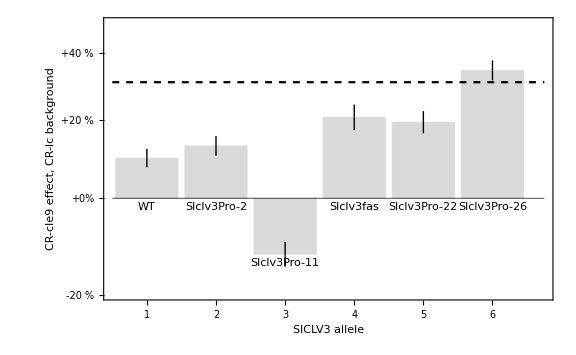

```mathematica
Transpose[{cle9logseffectslcbackground,Join[{"WT"},CLV3allelesByStrength]}]
Select[%,!(#[[1]]==="N/A")&]
Show[BarChart[%[[All,1]],Axes->{False,True},ChartStyle->LightGray,ChartLabels->Placed[%[[All,2]],Below (*,Rotate[#,45Degree]&*)],ImageSize->72 8,PlotRange->{{.5,6.75},{Log[.8],Log[1.5]}},FrameTicks->{{},Transpose[{Log[Range[.8,1.7,.1]],{"-20 %","-10 %","+0%","+10 %","+20 %","+30 %","+40 %","+50 %","+60 %",""}}]},Frame->{{True,False},{False,False}},FrameLabel->{"SlCLV3 allele","CR-cle9 effect, CR-lc background"},PlotRangePadding->False],
Plot[0,{x,.5,6.75},PlotStyle->{Black,AbsoluteThickness[.5]}],
Plot[effect["CR-cle9"]+c/.cle9sigmoidepistasis["BestFitParameters"],{x,.5,6.75},PlotStyle->{Black,Dashed}]](*Dashed line at level that the cle9 sigmoid epistasis model saturates*)
```

## Calculate supplemental tables (Supplemental Table S2)

Function for formatting the output:

```mathematica
FormatBlock[mat_]:=
Transpose[{
NumberForm[#,{4,3}]&/@mat[[All,1]],
NumberForm[#,{4,3}]&/@mat[[All,2]],
NumberForm[#,{4,3}]&/@mat[[All,3]],
If[#=="N/A","N/A",If[#<.0001,"<.0001",NumberForm[#,{5,4}]]]&/@mat[[All,4]]
}
]
```

### SlClv3^pro/CR-lc data

Calculate the rows in the table (underflow is due to very small p-values):

```mathematica
lcPairwiseInteractionTable=Table[
Table[
currentcounts={SelectFruits[{"WT"},{"WT"},{"WT"},{season}],
SelectFruits[{allele},{"WT"},{"WT"},{season}],
SelectFruits[{"WT"},{"SlwusCR-lc"},{"WT"},{season}],
SelectFruits[{allele},{"SlwusCR-lc"},{"WT"},{season}]};
If[Length[currentcounts[[2]]]>0&&Length[currentcounts[[1]]]>0&&allele!="WT",CalculatePairwiseEpistasis[Log[currentcounts]],ConstantArray["N/A",12]],{season,{"WestneckSummer2021","FLAFall2021"}}],
{allele,CLV3alleles[[allelicstrengthorder]][[2;;-2]]}];
```

General::munfl: Exp[-853.514] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-908.977] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-997.68] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Set column headings:

```mathematica
columnlabels={
"SlCLV3PRO allele",
"Slclv3Pro additive effect rep 1",
"Slclv3Pro additive effect 95% confidence interval lower rep 1",
"Slclv3Pro additive effect 95% confidence interval upper rep 1",
"Slclv3Pro additive effect p-value rep 1",
"Slclv3Pro additive effect rep 2",
"Slclv3Pro additive effect 95% confidence interval lower rep 2",
"Slclv3Pro additive effect 95% confidence interval upper rep 2",
"Slclv3Pro additive effect p-value rep 2",
"SlwusCR-lc additive effect rep 1",
"SlwusCR-lc additive effect 95% confidence interval lower rep 1",
"SlwusCR-lc additive effect 95% confidence interval upper rep 1",
"SlwusCR-lc additive effect p-value rep 1",
"SlwusCR-lc additive effect rep 2",
"SlwusCR-lc additive effect 95% confidence interval lower rep 2",
"SlwusCR-lc additive effect 95% confidence interval upper rep 2",
"SlwusCR-lc additive effect p-value rep 2",
"Slclv3Pro/SlwusCR-lc interaction effect rep 1",
"Slclv3Pro/SlwusCR-lc interaction 95% confidence interval lower rep 1",
"Slclv3Pro/SlwusCR-lc interaction 95% confidence interval upper rep 1",
"Slclv3Pro/SlwusCR-lc interaction p-value rep 1",
"Slclv3Pro/SlwusCR-lc interaction rep 2",
"Slclv3Pro/SlwusCR-lc interaction 95% confidence interval lower rep 2",
"Slclv3Pro/SlwusCR-lc interaction 95% confidence interval upper rep 2",
"Slclv3Pro/SlwusCR-lc interaction p-value rep 2"
};
```

Output table:

```mathematica
Export["Aguirre-etal-epistasis-SupplementalTableS2-lc.csv",Join[{columnlabels},
Table[Flatten[{CLV3alleles[[allelicstrengthorder]][[2;;-2]][[i]],
FormatBlock[lcPairwiseInteractionTable[[i,All,1;;4]]],
FormatBlock[lcPairwiseInteractionTable[[i,All,5;;8]]],
FormatBlock[lcPairwiseInteractionTable[[i,All,9;;12]]]}
],{i,11}]]]
```

Aguirre-etal-epistasis-SupplementalTableS2-lc.csv

### SlClv3^pro/Slcle9 data

Calculate the rows in the table (underflow is due to very small p-values):

```mathematica
cle9PairwiseInteractionTable=Table[
Table[
currentcounts={SelectFruits[{"WT"},{"WT"},{"WT"},{season}],
SelectFruits[{allele},{"WT"},{"WT"},{season}],
SelectFruits[{"WT"},{"WT"},{"Slcle9"},{season}],
SelectFruits[{allele},{"WT"},{"Slcle9"},{season}]};
If[Length[currentcounts[[2]]]>0&&Length[currentcounts[[1]]]>0&&allele!="WT",CalculatePairwiseEpistasis[Log[currentcounts]],ConstantArray["N/A",12]],{season,cle9Seasons}],
{allele,CLV3alleles[[allelicstrengthorder]][[2;;-2]]}];
```

General::munfl: Exp[-774.236] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-854.693] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1013.25] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

LinearModelFit::rank: The rank of the design matrix 3 is less than the number of terms 4 in the model. The model and results based upon it may contain significant numerical error.

Set column headings:

```mathematica
columnlabels={
"SlCLV3PRO allele",
"Slclv3Pro additive effect rep 1",
"Slclv3Pro additive effect 95% confidence interval lower rep 1",
"Slclv3Pro additive effect 95% confidence interval upper rep 1",
"Slclv3Pro additive effect p-value rep 1",
"Slclv3Pro additive effect rep 2",
"Slclv3Pro additive effect 95% confidence interval lower rep 2",
"Slclv3Pro additive effect 95% confidence interval upper rep 2",
"Slclv3Pro additive effect p-value rep 2",
"Slclv3Pro additive effect rep 3",
"Slclv3Pro additive effect 95% confidence interval lower rep 3",
"Slclv3Pro additive effect 95% confidence interval upper rep 3",
"Slclv3Pro additive effect p-value rep 3",
"Slcle9 additive effect rep 1",
"slcle9 additive effect 95% confidence interval lower rep 1",
"Slcle9 additive effect 95% confidence interval upper rep 1",
"Slcle9 additive effect p-value rep 1",
"Slcle9 additive effect rep 2",
"Slcle9 additive effect 95% confidence interval lower rep 2",
"Slcle9 additive effect 95% confidence interval upper rep 2",
"Slcle9 additive effect p-value rep 2",
"Slcle9 additive effect rep 3",
"Slcle9 additive effect 95% confidence interval lower rep 3",
"Slcle9 additive effect 95% confidence interval upper rep 3",
"Slcle9 additive effect p-value rep 3",
"Slclv3Pro/Slcle9 interaction effect rep 1",
"Slclv3Pro/Slcle9 interaction 95% confidence interval lower rep 1",
"Slclv3Pro/Slcle9 interaction 95% confidence interval upper rep 1",
"Slclv3Pro/Slcle9 interaction p-value rep 1",
"Slclv3Pro/Slcle9 interaction rep 2",
"Slclv3Pro/Slcle9 interaction 95% confidence interval lower rep 2",
"Slclv3Pro/Slcle9 interaction 95% confidence interval upper rep 2",
"Slclv3Pro/Slcle9 interaction p-value rep 2",
"Slclv3Pro/Slcle9 interaction rep 3",
"Slclv3Pro/Slcle9 interaction 95% confidence interval lower rep 3",
"Slclv3Pro/Slcle9 interaction 95% confidence interval upper rep 3",
"Slclv3Pro/Slcle9 interaction p-value rep 3"
};
```

Output table:

```mathematica
Export["Aguirre-etal-epistasis-SupplementalTableS2-cle9.csv",Join[{columnlabels},
Table[Flatten[{CLV3alleles[[allelicstrengthorder]][[2;;-2]][[i]],
FormatBlock[cle9PairwiseInteractionTable[[i,All,1;;4]]],
FormatBlock[cle9PairwiseInteractionTable[[i,All,5;;8]]],
FormatBlock[cle9PairwiseInteractionTable[[i,All,9;;12]]]}
],{i,11}]]]
```

Aguirre-etal-epistasis-SupplementalTableS2-cle9.csv

### Triple mutant data

Calculate all the rows in the table (underflow is due to very small p-values):

```mathematica
threewayTable=Table[{CalculateThreewayEpistasis[
Log[
{SelectFruits[{"WT"},{"WT"},{"WT"},{"FLASpring2022"}],
SelectFruits[{allele},{"WT"},{"WT"},{"FLASpring2022"}],
SelectFruits[{"WT"},{"SlwusCR-lc"},{"WT"},{"FLASpring2022"}],
SelectFruits[{"WT"},{"WT"},{"Slcle9"},{"FLASpring2022"}],
SelectFruits[{allele},{"SlwusCR-lc"},{"WT"},{"FLASpring2022"}],
SelectFruits[{allele},{"WT"},{"Slcle9"},{"FLASpring2022"}],
SelectFruits[{"WT"},{"SlwusCR-lc"},{"Slcle9"},{"FLASpring2022"}],
SelectFruits[{allele},{"SlwusCR-lc"},{"Slcle9"},{"FLASpring2022"}]}]]}
,{allele,{"Slclv3Pro-2","Slclv3Pro-11","Slclv3fas","Slclv3Pro-22","Slclv3Pro-26"}}];
```

General::munfl: Exp[-1028.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1618.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1954.04] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Set column headings:

```mathematica
columnlabels={
"SlCLV3PRO allele",
"Slclv3Pro additive effect",
"Slclv3Pro additive effect 95% confidence interval lower",
"Slclv3Pro additive effect 95% confidence interval upper",
"Slclv3Pro additive effect p-value",
"SlwusCR-lc additive effect",
"SlwusCR-lc additive effect 95% confidence interval lower",
"SlwusCR-lcadditive effect 95% confidence interval upper",
"SlwusCR-lc additive effect",
"Slcle9 additive effect",
"Slcle9 additive effect 95% confidence interval lower",
"Slcle9 additive effect 95% confidence interval upper",
"Slcle9 additive effect p-value",
"Slclv3Pro/SlwusCR-lc interaction effect",
"Slclv3Pro/SlwusCR-lc interaction 95% confidence interval lower",
"Slclv3Pro/SlwusCR-lc interaction 95% confidence interval upper",
"Slclv3Pro/SlwusCR-lc interaction p-value",
"Slclv3Pro/Slcle9 interaction effect",
"Slclv3Pro/Slcle9 interaction 95% confidence interval lower",
"Slclv3Pro/Slcle9 interaction 95% confidence interval upper",
"Slclv3Pro/Slcle9 interaction p-value",
"SlwusCR-lc/Slcle9 interaction effect",
"SlwusCR-lc/Slcle9 interaction 95% confidence interval lower",
"SlwusCR-lc/Slcle9 interaction 95% confidence interval upper",
"SlwusCR-lc/Slcle9 interaction p-value",
"Slclv3Pro/SlwusCR-lc/Slcle9 interaction effect",
"Slclv3Pro/SlwusCR-lc/Slcle9 interaction 95% confidence interval lower",
"Slclv3Pro/SlwusCR-lc/Slcle9 interaction 95% confidence interval upper",
"Slclv3Pro/SlwusCR-lc/Slcle9 interaction p-value"
};
Export["Aguirre-etal-epistasis-SupplementalTableS2-triples.csv",Join[{columnlabels},
Table[Flatten[{{"Slclv3Pro-2","Slclv3Pro-11","Slclv3fas","Slclv3Pro-22","Slclv3Pro-26"}[[i]],
FormatBlock[threewayTable[[i,All,1;;4]]],
FormatBlock[threewayTable[[i,All,5;;8]]],
FormatBlock[threewayTable[[i,All,9;;12]]],
FormatBlock[threewayTable[[i,All,13;;16]]],
FormatBlock[threewayTable[[i,All,17;;20]]],
FormatBlock[threewayTable[[i,All,21;;24]]],
FormatBlock[threewayTable[[i,All,25;;28]]]}
],{i,5}]]//TableForm]
```

Aguirre-etal-epistasis-SupplementalTableS2-triples.csv